Replace this with your own home directory:

```mathematica
yourdirectory = "/Users/lidar/Dropbox (Lidar group)/Apps/Overleaf/DD_paper"
```

/Users/lidar/Dropbox (Lidar group)/Apps/Overleaf/DD_paper

```mathematica
SetDirectory[yourdirectory]
```

/Users/lidar/Dropbox (Lidar group)/Apps/Overleaf/DD_paper

```mathematica
TP[a_,b_]:=KroneckerProduct[a,b];
Comm[a_,b_]:=a.b-b.a;
aComm[a_,b_]:=a.b+b.a;
```

Partial trace of a 4x4 matrix:

```mathematica
TrB[a_]:={{a[[1,1]]+a[[2,2]],a[[1,3]]+a[[2,4]]},{a[[3,1]]+a[[4,2]],a[[3,3]]+a[[4,4]]}};
```

The three Hamiltonians corresponding to the three rotating frames:

```mathematica
Hp=Δ/2 TP[PauliMatrix[0],PauliMatrix[3]]+J TP[PauliMatrix[3],PauliMatrix[3]]-(J+Δ/2)TP[PauliMatrix[0],PauliMatrix[0]];
Hp//MatrixForm
```

(0 | 0 | 0 | 0
0 | -2 J-Δ | 0 | 0
0 | 0 | -2 J | 0
0 | 0 | 0 | -Δ)

```mathematica
H0=-J TP[PauliMatrix[3],PauliMatrix[0]]+ (Δ/2-J) TP[PauliMatrix[0],PauliMatrix[3]]+J TP[PauliMatrix[3],PauliMatrix[3]]-(-J+Δ/2)TP[PauliMatrix[0],PauliMatrix[0]];
H0//MatrixForm
```

(0 | 0 | 0 | 0
0 | -Δ | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 4 J-Δ)

```mathematica
H1=J TP[PauliMatrix[3],PauliMatrix[0]]+ (Δ/2+J) TP[PauliMatrix[0],PauliMatrix[3]]+J TP[PauliMatrix[3],PauliMatrix[3]]-(3J+Δ/2)TP[PauliMatrix[0],PauliMatrix[0]];
H1//MatrixForm
```

(0 | 0 | 0 | 0
0 | -4 J-Δ | 0 | 0
0 | 0 | -4 J | 0
0 | 0 | 0 | -4 J-Δ)

Dephasing Lindblad operators:

```mathematica
L1=TP[PauliMatrix[3],PauliMatrix[0]];
L2=TP[PauliMatrix[0],PauliMatrix[3]];
L12=TP[PauliMatrix[3],PauliMatrix[3]];
```

X-flip Lindblad operators:

```mathematica
L1x=TP[PauliMatrix[1],PauliMatrix[0]];
L2x=TP[PauliMatrix[0],PauliMatrix[1]];
L12x=TP[PauliMatrix[1],PauliMatrix[1]];
```

Y-flip Lindblad operators:

```mathematica
L1y=TP[PauliMatrix[2],PauliMatrix[0]];
L2y=TP[PauliMatrix[0],PauliMatrix[2]];
L12y=TP[PauliMatrix[2],PauliMatrix[2]];
```

Amplitude damping Lindblad operators:

```mathematica
damp01={{0,1},{0,0}};
```

```mathematica
L1d=TP[damp01,PauliMatrix[0]];
L2d=TP[PauliMatrix[0],damp01];
L12d=TP[damp01,damp01];
```

The full Lindbladian: 
(note that the IZ rate (called γ2) isn’t expected to play a role after tracing out the spectator qubit, hence it’s not a variable that’s listed in the Dephase case)

```mathematica
Lind[L_,x_]:=L.x.ConjugateTranspose[L]-(1/2)aComm[ConjugateTranspose[L].L,x];
```

```mathematica
Dephase[H_,ρ_,γ1_,γ3_]:=-I Comm[H,ρ]+γ1 Lind[L1,ρ]+γ2 Lind[L2,ρ]+γ3 Lind[L12,ρ];
```

```mathematica
Decohere[H_,ρ_,γ1_,γ2_,γ3_,γ1x_,γ2x_,γ3x_,γ1y_,γ2y_,γ3y_]:=-I Comm[H,ρ]+γ1 Lind[L1,ρ]+γ2 Lind[L2,ρ]+γ3 Lind[L12,ρ]+γ1x Lind[L1x,ρ]+γ2x Lind[L2x,ρ]+γ3x Lind[L12x,ρ]+γ1y Lind[L1y,ρ]+γ2y Lind[L2y,ρ]+γ3y Lind[L12y,ρ];
```

A generic 4x4 matrix:

```mathematica
rho[t_]:={{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}};
rho[t]//MatrixForm
```

(r11[t] | r12[t] | r13[t] | r14[t]
r21[t] | r22[t] | r23[t] | r24[t]
r31[t] | r32[t] | r33[t] | r34[t]
r41[t] | r42[t] | r43[t] | r44[t])

The |+> state:

```mathematica
ketp={1,1}/Sqrt[2];
```

The three initial states of the main and spectator qubit. Main qubit is in |+>, spectator is in |+>, |0>, or |1>:

```mathematica
ketpp={1,1,1,1}/2;
ketp0={1,0,1,0}/Sqrt[2];
ketp1={0,1,0,1}/Sqrt[2];
```

```mathematica
rhopp=TP[ketpp,ketpp];
rhop0=TP[ketp0,ketp0];
rhop1=TP[ketp1,ketp1];
```

## Pure dephasing

Pure dephasing results for the H^+ Hamiltonian:

The first line solves the Lindblad equation with the initial condition set to |++>:

```mathematica
rhototpp[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Dephase[Hp,rho[t],γ1,γ3][[i,j]],rho[0][[i,j]]==rhopp[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
solrhopp[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototpp[t])[[1]]//FullSimplify;
solrhopp[t]//MatrixForm
rhoSpp[t_]=TrB[solrhopp[t]]//FullSimplify;
rhoSpp[t]//MatrixForm
fidpp[t_]=ketp.rhoSpp[t].ketp//FullSimplify
```

(1/4 | 1/4 ⅇ^(-ⅈ t (2 J-2 ⅈ (γ2+γ3)+Δ)) | 1/4 ⅇ^(-2 ⅈ J t-2 t (γ1+γ3)) | 1/4 ⅇ^(-2 t (γ1+γ2)-ⅈ t Δ)
1/4 ⅇ^(ⅈ t (2 J+2 ⅈ (γ2+γ3)+Δ)) | 1/4 | 1/4 ⅇ^(-2 t (γ1+γ2)+ⅈ t Δ) | 1/4 ⅇ^(2 ⅈ t (J+ⅈ (γ1+γ3)))
1/4 ⅇ^(2 ⅈ t (J+ⅈ (γ1+γ3))) | 1/4 ⅇ^(-2 t (γ1+γ2)-ⅈ t Δ) | 1/4 | 1/4 ⅇ^(t (2 ⅈ J-2 (γ2+γ3)-ⅈ Δ))
1/4 ⅇ^(-2 t (γ1+γ2)+ⅈ t Δ) | 1/4 ⅇ^(-2 ⅈ J t-2 t (γ1+γ3)) | 1/4 ⅇ^(t (-2 ⅈ J-2 (γ2+γ3)+ⅈ Δ)) | 1/4)

(1/2 | 1/2 ⅇ^(-2 t (γ1+γ3)) Cos[2 J t]
1/2 ⅇ^(-2 t (γ1+γ3)) Cos[2 J t] | 1/2)

1/2 (1+ⅇ^(-2 t (γ1+γ3)) Cos[2 J t])

```mathematica
fidppZ[t_,J_,γ1_,γ2_,γ3_](*=fidpp[t]*):=1/2 (1+ⅇ^(-2 t (γ1+γ3)) Cos[2 J t])
```

The first line solves the Lindblad equation with the initial condition set to |+0>. The last line shows the result is identical to the case with the |++> initial condition.

```mathematica
rhototp0[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Dephase[Hp,rho[t],γ1,γ3][[i,j]],rho[0][[i,j]]==rhop0[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
solrhop0[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototp0[t])[[1]]//FullSimplify;
solrhop0[t]//MatrixForm
rhoSp0[t_]=TrB[solrhop0[t]]//FullSimplify;
rhoSp0[t]//MatrixForm
fidp0[t_]=FullSimplify[ketp.rhoSp0[t].ketp//TrigExpand,Assumptions->{t,J,γ1,γ2}∈Reals]
fidpp[t]-fidp0[t]//FullSimplify
```

(1/2 | 0 | 1/2 ⅇ^(-2 ⅈ J t-2 t (γ1+γ3)) | 0
0 | 0 | 0 | 0
1/2 ⅇ^(2 ⅈ t (J+ⅈ (γ1+γ3))) | 0 | 1/2 | 0
0 | 0 | 0 | 0)

(1/2 | 1/2 ⅇ^(-2 ⅈ J t-2 t (γ1+γ3))
1/2 ⅇ^(2 ⅈ t (J+ⅈ (γ1+γ3))) | 1/2)

1/4 (2+ⅇ^(-2 t (ⅈ J+γ1+γ3)) (1+ⅇ^(4 ⅈ J t)))

0

The first line solves the Lindblad equation with the initial condition set to |+1>. The last line shows the result is identical to the case with the |++> initial condition.

```mathematica
rhototp1[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Dephase[Hp,rho[t],γ1,γ3][[i,j]],rho[0][[i,j]]==rhop1[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
solrhop1[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototp1[t])[[1]]//FullSimplify;
solrhop1[t]//MatrixForm
rhoSp1[t_]=TrB[solrhop1[t]]//FullSimplify;
rhoSp1[t]//MatrixForm
fidp1[t_]=ketp.rhoSp1[t].ketp//FullSimplify
fidpp[t]-fidp1[t]//FullSimplify
```

(0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2 ⅇ^(2 ⅈ t (J+ⅈ (γ1+γ3)))
0 | 0 | 0 | 0
0 | 1/2 ⅇ^(-2 ⅈ J t-2 t (γ1+γ3)) | 0 | 1/2)

(1/2 | 1/2 ⅇ^(2 ⅈ t (J+ⅈ (γ1+γ3)))
1/2 ⅇ^(-2 ⅈ J t-2 t (γ1+γ3)) | 1/2)

1/4 (2+ⅇ^(-2 t (ⅈ J+γ1+γ3)) (1+ⅇ^(4 ⅈ J t)))

0

Results for the H^0 Hamiltonian:

```mathematica
rhototpp[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Dephase[H0,rho[t],γ1,γ3][[i,j]],rho[0][[i,j]]==rhopp[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
solrhopp[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototpp[t])[[1]]//FullSimplify;
solrhopp[t]//MatrixForm
rhoSpp[t_]=TrB[solrhopp[t]]//FullSimplify;
rhoSpp[t]//MatrixForm
fidpp[t_]=ketp.rhoSpp[t].ketp//FullSimplify
fidpp[t]-1/2 (1+Exp[-2t(γ1+γ3)]Cos[2J t]^2)//FullSimplify
fidpp[t]-1/2 (1+Exp[-2t(γ1+γ3)](Cos[4J t]+1)/2)//FullSimplify
```

(1/4 | 1/4 ⅇ^(-2 t (γ2+γ3)-ⅈ t Δ) | 1/4 ⅇ^(-2 t (γ1+γ3)) | 1/4 ⅇ^(t (4 ⅈ J-2 (γ1+γ2)-ⅈ Δ))
1/4 ⅇ^(-2 t (γ2+γ3)+ⅈ t Δ) | 1/4 | 1/4 ⅇ^(-2 t (γ1+γ2)+ⅈ t Δ) | 1/4 ⅇ^(4 ⅈ J t-2 t (γ1+γ3))
1/4 ⅇ^(-2 t (γ1+γ3)) | 1/4 ⅇ^(-2 t (γ1+γ2)-ⅈ t Δ) | 1/4 | 1/4 ⅇ^(t (4 ⅈ J-2 (γ2+γ3)-ⅈ Δ))
1/4 ⅇ^(t (-4 ⅈ J-2 (γ1+γ2)+ⅈ Δ)) | 1/4 ⅇ^(-4 ⅈ J t-2 t (γ1+γ3)) | 1/4 ⅇ^(t (-4 ⅈ J-2 (γ2+γ3)+ⅈ Δ)) | 1/4)

(1/2 | 1/4 ⅇ^(-2 t (γ1+γ3)) (1+ⅇ^(4 ⅈ J t))
1/4 ⅇ^(-2 t (2 ⅈ J+γ1+γ3)) (1+ⅇ^(4 ⅈ J t)) | 1/2)

1/8 (4+ⅇ^(-2 t (2 ⅈ J+γ1+γ3)) (1+ⅇ^(4 ⅈ J t))^2)

0

0

```mathematica
rhototp0[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Dephase[H0,rho[t],γ1,γ3][[i,j]],rho[0][[i,j]]==rhop0[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
solrhop0[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototp0[t])[[1]]//FullSimplify;
solrhop0[t]//MatrixForm
rhoSp0[t_]=TrB[solrhop0[t]]//FullSimplify;
rhoSp0[t]//MatrixForm
fidp0[t_]=FullSimplify[ketp.rhoSp0[t].ketp//TrigExpand,Assumptions->{t,J,γ1,γ2}∈Reals]
```

(1/2 | 0 | 1/2 ⅇ^(-2 t (γ1+γ3)) | 0
0 | 0 | 0 | 0
1/2 ⅇ^(-2 t (γ1+γ3)) | 0 | 1/2 | 0
0 | 0 | 0 | 0)

(1/2 | 1/2 ⅇ^(-2 t (γ1+γ3))
1/2 ⅇ^(-2 t (γ1+γ3)) | 1/2)

1/2 (1+ⅇ^(-2 t (γ1+γ3)))

```mathematica
rhototp1[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Dephase[H0,rho[t],γ1,γ3][[i,j]],rho[0][[i,j]]==rhop1[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
solrhop1[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototp1[t])[[1]]//FullSimplify;
solrhop1[t]//MatrixForm
rhoSp1[t_]=TrB[solrhop1[t]]//FullSimplify;
rhoSp1[t]//MatrixForm
fidp1[t_]=ketp.rhoSp1[t].ketp//FullSimplify
fidp1[t]-1/2 (1+Exp[-2t(γ1+γ3)]Cos[4J t])//FullSimplify
```

(0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2 ⅇ^(4 ⅈ J t-2 t (γ1+γ3))
0 | 0 | 0 | 0
0 | 1/2 ⅇ^(-4 ⅈ J t-2 t (γ1+γ3)) | 0 | 1/2)

(1/2 | 1/2 ⅇ^(4 ⅈ J t-2 t (γ1+γ3))
1/2 ⅇ^(-4 ⅈ J t-2 t (γ1+γ3)) | 1/2)

1/4 (2+ⅇ^(-2 t (2 ⅈ J+γ1+γ3)) (1+ⅇ^(8 ⅈ J t)))

0

## Dephasing plus X-flips

Results for the H^+ Hamiltonian with X-flips:

Results for the |++> initial state:

```mathematica
rhototpp[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,γ1x,γ2x,γ3x,0,0,0][[i,j]],rho[0][[i,j]]==rhopp[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t]
```

{{r11[t]→1/4,r22[t]→1/4,12,r32[t]→-((ⅇ^(t (-2 γ1-2 γ1x-2 γ2-γ2x-γ3x-√(γ2x^2-2 γ2x γ3x+γ3x^2-Δ^2))) γ1x^8 γ2x^3 √(γ2x^2-2 γ2x γ3x+γ3x^2-Δ^2)-ⅇ^(t (-2 γ1-2 γ1x-2 γ2-γ2x-γ3x+√(γ2x^2-2 γ2x γ3x+γ3x^2-Δ^2))) γ1x^8 γ2x^3 √(γ2x^2-2 γ2x γ3x+γ3x^2-Δ^2)-2 ⅇ^(t (1)) γ1x^6 γ2x^5 √(γ2x^2-2 γ2x γ3x+γ3x^2-Δ^2)+280+ⅇ^(t (1)) γ1x^4 γ3x Δ^6 √(γ2x^2+2 γ2x γ3x+γ3x^2-Δ^2)-ⅇ^(t (-2 γ1-2 γ2-γ2x-γ3x+√(γ2x^2+2 γ2x γ3x+γ3x^2-Δ^2))) γ1x^4 γ3x Δ^6 √(γ2x^2+2 γ2x γ3x+γ3x^2-Δ^2))/(16 (γ1x γ2x^2-2 γ1x γ2x γ3x+γ1x γ3x^2-γ1x Δ^2+γ1x^2 √(γ2x^2-2 γ2x γ3x+γ3x^2-Δ^2)-γ2x γ3x √(γ2x^2-2 γ2x γ3x+γ3x^2-Δ^2)) (γ1x γ2x^2-2 γ1x γ2x γ3x+γ1x 1-1-γ1x^2 √1+γ2x γ3x √(γ2x^2-2 γ2x γ3x+γ3x^2-Δ^2)) (γ1x γ2x^2+2 γ1x γ2x γ3x+γ1x γ3x^2-γ1x Δ^2+γ1x^2 √(γ2x^2+2 γ2x γ3x+γ3x^2-Δ^2)+γ2x γ3x √(γ2x^2+2 γ2x γ3x+γ3x^2-Δ^2)) (-γ1x γ2x^2-2 γ1x γ2x γ3x-γ1x γ3x^2+γ1x Δ^2+γ1x^2 √(γ2x^2+2 γ2x γ3x+γ3x^2-Δ^2)+γ2x γ3x √(γ2x^2+2 γ2x γ3x+γ3x^2-Δ^2))))-1/1-1-1/1,r41[t]→1}}
 |  |  |  |

```mathematica
solrhopp[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototpp[t])[[1]];
solrhopp[t]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
rhoSpp[t_]=TrB[solrhopp[t]];
rhoSpp[t]//MatrixForm
```

(1/2 | 1
1 | 1/2)
 |  |  |  |

```mathematica
fidpp[t_]=ketp.rhoSpp[t].ketp//FullSimplify
```

(ⅇ^(-t (2 γ1+γ1x+γ2x+√(-4 J^2+(γ1x+γ2x)^2)+2 γ3)) (-4 (1+ⅇ^(2 t √(-4 J^2+(γ1x+γ2x)^2))+2 ⅇ^(t (2 γ1+γ1x+γ2x+√(-4 J^2+(γ1x+γ2x)^2)+2 γ3))) J^2+(γ1x+γ2x) (2 ⅇ^(t (2 γ1+γ1x+γ2x+√(-4 J^2+(γ1x+γ2x)^2)+2 γ3)) (γ1x+γ2x)+(1+ⅇ^(2 t √(-4 J^2+(γ1x+γ2x)^2))) (γ1x+γ2x)-√(-4 J^2+(γ1x+γ2x)^2)+ⅇ^(2 t √(-4 J^2+(γ1x+γ2x)^2)) √(-4 J^2+(γ1x+γ2x)^2))))/(4 (-2 J+γ1x+γ2x) (2 J+γ1x+γ2x))

```mathematica
fidpp[0]//FullSimplify
```

1

```mathematica
FullSimplify[1/2 (1+ⅇ^(-t (2 γ1+γ1x+γ2x+2 γ3)) (Cos[t √(4 J^2-(γ1x+γ2x)^2)]+((γ1x+γ2x) Sin[t √(4 J^2-(γ1x+γ2x)^2)])/(√(4 J^2-(γ1x+γ2x)^2))))-fidpp[t],Assumptions->{4 J^2-(γ1x+γ2x)>0}]
```

Piecewise[{{0, 4 J^2>(γ1x+γ2x)^2}, {1/2 ⅇ^(-t (2 γ1+γ1x+γ2x+2 γ3)) (Cos[t √(4 J^2-(γ1x+γ2x)^2)]-Cosh[t √(-4 J^2+(γ1x+γ2x)^2)]+((γ1x+γ2x) (Sin[t √(4 J^2-(γ1x+γ2x)^2)]-ⅈ Sinh[t √(-4 J^2+(γ1x+γ2x)^2)]))/(√(4 J^2-(γ1x+γ2x)^2))), True}}]

```mathematica
fidppZX[t_,J_,γ1_,γ2_,γ3_,γ1x_,γ2x_,γ3x_](*=fidpp[t]*):=1/2 (1+ⅇ^(-t (2 γ1+γ1x+γ2x+2 γ3)) (Cos[t √(4 J^2-(γ1x+γ2x)^2)]+((γ1x+γ2x) Sin[t √(4 J^2-(γ1x+γ2x)^2)])/(√(4 J^2-(γ1x+γ2x)^2))));
```

Results for the |+0> initial state. The last line shows the result is identical to the case with the |++> initial condition.

```mathematica
rhototp0[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,γ1x,γ2x,γ3x,0,0,0][[i,j]],rho[0][[i,j]]==rhop0[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
```

```mathematica
solrhop0[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototp0[t])[[1]];
```

```mathematica
solrhop0[t]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
rhoSp0[t_]=TrB[solrhop0[t]];
rhoSp0[t]//MatrixForm
```

(1/4 ⅇ^(-2 t (γ2x+γ3x)) (-1+ⅇ^(2 t (γ2x+γ3x)))+1/4 ⅇ^(-2 t (γ2x+γ3x)) (1+ⅇ^(2 t (γ2x+γ3x))) | -(16 ⅇ^(t (-2 γ1-γ1x-γ2x-√(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2)-2 γ3)) J^4 γ1x^4 γ2x^4+16 ⅇ^(t (-2 γ1-γ1x-γ2x+√(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2)-2 γ3)) J^4 γ1x^4 γ2x^4+16 ⅇ^(t (1)) J^4 γ1x^4 γ2x^4+517+4 ⅈ 5 γ3x^8+2 ⅈ ⅇ^(t (-2 γ1-γ1x-γ2x-√1-2 γ3)) J γ2x^2 √(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2) γ3x^8-2 ⅈ ⅇ^(t (-2 γ1-γ1x-γ2x+√(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2)-2 γ3)) J γ2x^2 √(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2) γ3x^8)/(8 (γ1x γ2x √(-4 J^2+γ1x^2-2 γ1x γ2x+γ2x^2)+4 J^2 γ3x-γ1x^2 γ3x+2 γ1x γ2x γ3x-γ2x^2 γ3x-√(-4 J^2+γ1x^2-2 γ1x γ2x+γ2x^2) γ3x^2) (1) (-γ1x γ2x √(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2)-4 J^2 γ3x+γ1x^2 γ3x+2 γ1x γ2x γ3x+γ2x^2 γ3x-√(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2) γ3x^2) (γ1x γ2x √(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2)-4 J^2 γ3x+γ1x^2 γ3x+2 γ1x γ2x γ3x+γ2x^2 γ3x+√(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2) γ3x^2))-1/1+1/1-1/(8 3 (6+1))
1 | 1)
 |  |  |  |

```mathematica
fidp0[t_]=ketp.rhoSp0[t].ketp//FullSimplify
```

(ⅇ^(-t (2 γ1+γ1x+γ2x+√(-4 J^2+(γ1x+γ2x)^2)+2 γ3)) (-4 (1+ⅇ^(2 t √(-4 J^2+(γ1x+γ2x)^2))+2 ⅇ^(t (2 γ1+γ1x+γ2x+√(-4 J^2+(γ1x+γ2x)^2)+2 γ3))) J^2+(γ1x+γ2x) (2 ⅇ^(t (2 γ1+γ1x+γ2x+√(-4 J^2+(γ1x+γ2x)^2)+2 γ3)) (γ1x+γ2x)+(1+ⅇ^(2 t √(-4 J^2+(γ1x+γ2x)^2))) (γ1x+γ2x)-√(-4 J^2+(γ1x+γ2x)^2)+ⅇ^(2 t √(-4 J^2+(γ1x+γ2x)^2)) √(-4 J^2+(γ1x+γ2x)^2))))/(4 (-2 J+γ1x+γ2x) (2 J+γ1x+γ2x))

```mathematica
fidpp[t]-fidp0[t]//FullSimplify
```

0

Results for the |+1> initial state. The last line shows the result is identical to the case with the |++> initial condition.

```mathematica
rhototp1[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,γ1x,γ2x,γ3x,0,0,0][[i,j]],rho[0][[i,j]]==rhop1[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
```

```mathematica
solrhop1[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototp1[t])[[1]];
solrhop1[t]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
rhoSp1[t_]=TrB[solrhop1[t]];
rhoSp1[t]//MatrixForm
```

(1/4 ⅇ^(-2 t (γ2x+γ3x)) (-1+ⅇ^(2 t (γ2x+γ3x)))+1/4 ⅇ^(-2 t (γ2x+γ3x)) (1+ⅇ^(2 t (γ2x+γ3x))) | -(16 ⅇ^(t (-2 γ1-γ1x-γ2x-√(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2)-2 γ3)) J^4 γ1x^4 γ2x^4+529+4 ⅈ 5 γ3x^8+2 ⅈ ⅇ^(t (-2 γ1-γ1x-γ2x-√1-2 γ3)) J γ2x^2 √(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2) γ3x^8-2 ⅈ ⅇ^(t (-2 γ1-γ1x-γ2x+√(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2)-2 γ3)) J γ2x^2 √(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2) γ3x^8)/(8 (γ1x γ2x √(-4 J^2+γ1x^2-2 γ1x γ2x+γ2x^2)+4 J^2 γ3x-γ1x^2 γ3x+2 γ1x γ2x γ3x-γ2x^2 γ3x-√(-4 J^2+γ1x^2-2 γ1x γ2x+γ2x^2) γ3x^2) (1) (-γ1x γ2x √(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2)-4 J^2 γ3x+γ1x^2 γ3x+2 γ1x γ2x γ3x+γ2x^2 γ3x-√(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2) γ3x^2) (γ1x γ2x √(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2)-4 J^2 γ3x+γ1x^2 γ3x+2 γ1x γ2x γ3x+γ2x^2 γ3x+√(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2) γ3x^2))-1/(8 3 (1))+1/1-(287+1)/(8 3 (γ1x γ2x √(-4 J^2+γ1x^2+2 γ1x γ2x+γ2x^2)-4 J^2 γ3x+2+1+√1 γ3x^2))
1 | 1)
 |  |  |  |

```mathematica
fidp1[t_]=ketp.rhoSp1[t].ketp//FullSimplify
```

(ⅇ^(-t (2 γ1+γ1x+γ2x+√(-4 J^2+(γ1x+γ2x)^2)+2 γ3)) (-4 (1+ⅇ^(2 t √(-4 J^2+(γ1x+γ2x)^2))+2 ⅇ^(t (2 γ1+γ1x+γ2x+√(-4 J^2+(γ1x+γ2x)^2)+2 γ3))) J^2+(γ1x+γ2x) (2 ⅇ^(t (2 γ1+γ1x+γ2x+√(-4 J^2+(γ1x+γ2x)^2)+2 γ3)) (γ1x+γ2x)+(1+ⅇ^(2 t √(-4 J^2+(γ1x+γ2x)^2))) (γ1x+γ2x)-√(-4 J^2+(γ1x+γ2x)^2)+ⅇ^(2 t √(-4 J^2+(γ1x+γ2x)^2)) √(-4 J^2+(γ1x+γ2x)^2))))/(4 (-2 J+γ1x+γ2x) (2 J+γ1x+γ2x))

```mathematica
fidpp[t]-fidp1[t]//FullSimplify
```

0

## Dephasing plus Y - flips

Results for the H^+ Hamiltonian with Y flips:

Results for the |++> initial state:

```mathematica
rhototpp[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,0,0,0,γ1y,γ2y,γ3y][[i,j]],rho[0][[i,j]]==rhopp[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t]
```

{{r11[t]→1/4,r22[t]→1/4,12,r32[t]→-((ⅇ^(t (-2 γ1-2 γ1y-2 γ2-γ2y-γ3y-√(γ2y^2-2 γ2y γ3y+γ3y^2-Δ^2))) γ1y^8 γ2y^3 √(γ2y^2-2 γ2y γ3y+γ3y^2-Δ^2)-ⅇ^(t (-2 γ1-2 γ1y-2 γ2-γ2y-γ3y+√(γ2y^2-2 γ2y γ3y+γ3y^2-Δ^2))) γ1y^8 γ2y^3 √(γ2y^2-2 γ2y γ3y+γ3y^2-Δ^2)-2 ⅇ^(t (1)) γ1y^6 γ2y^5 √(γ2y^2-2 γ2y γ3y+γ3y^2-Δ^2)+280+ⅇ^(t (1)) γ1y^4 γ3y Δ^6 √(γ2y^2+2 γ2y γ3y+γ3y^2-Δ^2)-ⅇ^(t (-2 γ1-2 γ2-γ2y-γ3y+√(γ2y^2+2 γ2y γ3y+γ3y^2-Δ^2))) γ1y^4 γ3y Δ^6 √(γ2y^2+2 γ2y γ3y+γ3y^2-Δ^2))/(16 (γ1y γ2y^2-2 γ1y γ2y γ3y+γ1y γ3y^2-γ1y Δ^2+γ1y^2 √(γ2y^2-2 γ2y γ3y+γ3y^2-Δ^2)-γ2y γ3y √(γ2y^2-2 γ2y γ3y+γ3y^2-Δ^2)) (γ1y γ2y^2-2 γ1y γ2y γ3y+γ1y 1-1-γ1y^2 √1+γ2y γ3y √(γ2y^2-2 γ2y γ3y+γ3y^2-Δ^2)) (γ1y γ2y^2+2 γ1y γ2y γ3y+γ1y γ3y^2-γ1y Δ^2+γ1y^2 √(γ2y^2+2 γ2y γ3y+γ3y^2-Δ^2)+γ2y γ3y √(γ2y^2+2 γ2y γ3y+γ3y^2-Δ^2)) (-γ1y γ2y^2-2 γ1y γ2y γ3y-γ1y γ3y^2+γ1y Δ^2+γ1y^2 √(γ2y^2+2 γ2y γ3y+γ3y^2-Δ^2)+γ2y γ3y √(γ2y^2+2 γ2y γ3y+γ3y^2-Δ^2))))-1/1-1-1/1,r41[t]→1}}
 |  |  |  |

```mathematica
solrhopp[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototpp[t])[[1]];
solrhopp[t]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
rhoSpp[t_]=TrB[solrhopp[t]];
rhoSpp[t]//MatrixForm
```

(1/2 | 1
1 | 1/2)
 |  |  |  |

```mathematica
fidpp[t_]=ketp.rhoSpp[t].ketp//FullSimplify
```

1/(4 (-4 J^2+(γ1y-γ2y)^2))ⅇ^(-t (2 γ1+γ1y+√(-4 J^2+(γ1y-γ2y)^2)+γ2y+2 (γ3+γ3y))) (-4 (1+ⅇ^(2 t √(-4 J^2+(γ1y-γ2y)^2))+2 ⅇ^(t (2 γ1+γ1y+√(-4 J^2+(γ1y-γ2y)^2)+γ2y+2 (γ3+γ3y)))) J^2+(√(-4 J^2+(γ1y-γ2y)^2)-ⅇ^(2 t √(-4 J^2+(γ1y-γ2y)^2)) √(-4 J^2+(γ1y-γ2y)^2)+2 ⅇ^(t (2 γ1+γ1y+√(-4 J^2+(γ1y-γ2y)^2)+γ2y+2 (γ3+γ3y))) (γ1y-γ2y)+(1+ⅇ^(2 t √(-4 J^2+(γ1y-γ2y)^2))) (γ1y-γ2y)) (γ1y-γ2y))

```mathematica
fidpp[0]
```

1

```mathematica
fidppZY[t_,J_,γ1_,γ2_,γ3_,γ1y_,γ2y_,γ3y_](*=fidpp[t]*):=1/2+1/2 ⅇ^(-t (2 γ1+γ1y+γ2y+2 (γ3+γ3y))) (Cos[t √(4 J^2-(γ1y-γ2y)^2)]+((-γ1y+γ2y) Sin[t √(4 J^2-(γ1y-γ2y)^2)])/(√(4 J^2-(γ1y-γ2y)^2)))
```

Results for the |+0> initial state. The last line shows the result is identical to the case with the |++> initial condition.

```mathematica
rhototp0[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,0,0,0,γ1y,γ2y,γ3y][[i,j]],rho[0][[i,j]]==rhop0[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
```

```mathematica
solrhop0[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototp0[t])[[1]];
```

```mathematica
solrhop0[t]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
rhoSp0[t_]=TrB[solrhop0[t]];
rhoSp0[t]//MatrixForm
```

(1/4 ⅇ^(-2 t (γ2y+γ3y)) (-1+ⅇ^(2 t (γ2y+γ3y)))+1/4 ⅇ^(-2 t (γ2y+γ3y)) (1+ⅇ^(2 t (γ2y+γ3y))) | -(16 ⅇ^(t (-2 γ1-γ1y-γ2y-√(-4 J^2+γ1y^2+2 γ1y γ2y+γ2y^2)-2 γ3)) J^4 γ1y^4 γ2y^4+16 ⅇ^(t (-2 γ1-γ1y-γ2y+√(-4 J^2+γ1y^2+2 γ1y γ2y+γ2y^2)-2 γ3)) J^4 γ1y^4 γ2y^4+16 ⅇ^(t (1)) J^4 γ1y^4 γ2y^4+517+4 ⅈ 5 γ3y^8+2 ⅈ ⅇ^(t (-2 γ1-γ1y-γ2y-√1-2 γ3)) J γ2y^2 √(-4 J^2+γ1y^2+2 γ1y γ2y+γ2y^2) γ3y^8-2 ⅈ ⅇ^(t (-2 γ1-γ1y-γ2y+√(-4 J^2+γ1y^2+2 γ1y γ2y+γ2y^2)-2 γ3)) J γ2y^2 √(-4 J^2+γ1y^2+2 γ1y γ2y+γ2y^2) γ3y^8)/(8 (γ1y γ2y √(-4 J^2+γ1y^2-2 γ1y γ2y+γ2y^2)+4 J^2 γ3y-γ1y^2 γ3y+2 γ1y γ2y γ3y-γ2y^2 γ3y-√(-4 J^2+γ1y^2-2 γ1y γ2y+γ2y^2) γ3y^2) (1) (-γ1y γ2y √(-4 J^2+γ1y^2+2 γ1y γ2y+γ2y^2)-4 J^2 γ3y+γ1y^2 γ3y+2 γ1y γ2y γ3y+γ2y^2 γ3y-√(-4 J^2+γ1y^2+2 γ1y γ2y+γ2y^2) γ3y^2) (γ1y γ2y √(-4 J^2+γ1y^2+2 γ1y γ2y+γ2y^2)-4 J^2 γ3y+γ1y^2 γ3y+2 γ1y γ2y γ3y+γ2y^2 γ3y+√(-4 J^2+γ1y^2+2 γ1y γ2y+γ2y^2) γ3y^2))-1/1+1/1-1/(8 3 (6+1))
1 | 1)
 |  |  |  |

```mathematica
fidp0[t_]=ketp.rhoSp0[t].ketp//FullSimplify
```

1/(4 (-4 J^2+(γ1y-γ2y)^2))ⅇ^(-t (2 γ1+γ1y+√(-4 J^2+(γ1y-γ2y)^2)+γ2y+2 (γ3+γ3y))) (-4 (1+ⅇ^(2 t √(-4 J^2+(γ1y-γ2y)^2))+2 ⅇ^(t (2 γ1+γ1y+√(-4 J^2+(γ1y-γ2y)^2)+γ2y+2 (γ3+γ3y)))) J^2+(√(-4 J^2+(γ1y-γ2y)^2)-ⅇ^(2 t √(-4 J^2+(γ1y-γ2y)^2)) √(-4 J^2+(γ1y-γ2y)^2)+2 ⅇ^(t (2 γ1+γ1y+√(-4 J^2+(γ1y-γ2y)^2)+γ2y+2 (γ3+γ3y))) (γ1y-γ2y)+(1+ⅇ^(2 t √(-4 J^2+(γ1y-γ2y)^2))) (γ1y-γ2y)) (γ1y-γ2y))

```mathematica
fidpp[t]-fidp0[t]//FullSimplify
```

0

Results for the |+1> initial state. The last line shows the result is identical to the case with the |++> initial condition.

```mathematica
rhototp1[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,0,0,0,γ1y,γ2y,γ3y][[i,j]],rho[0][[i,j]]==rhop1[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
```

```mathematica
solrhop1[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototp1[t])[[1]];
solrhop1[t]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
rhoSp1[t_]=TrB[solrhop1[t]];
rhoSp1[t]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
fidp1[t_]=ketp.rhoSp1[t].ketp//FullSimplify
```

1/(4 (-4 J^2+(γ1y-γ2y)^2))ⅇ^(-t (2 γ1+γ1y+√(-4 J^2+(γ1y-γ2y)^2)+γ2y+2 (γ3+γ3y))) (-4 (1+ⅇ^(2 t √(-4 J^2+(γ1y-γ2y)^2))+2 ⅇ^(t (2 γ1+γ1y+√(-4 J^2+(γ1y-γ2y)^2)+γ2y+2 (γ3+γ3y)))) J^2+(√(-4 J^2+(γ1y-γ2y)^2)-ⅇ^(2 t √(-4 J^2+(γ1y-γ2y)^2)) √(-4 J^2+(γ1y-γ2y)^2)+2 ⅇ^(t (2 γ1+γ1y+√(-4 J^2+(γ1y-γ2y)^2)+γ2y+2 (γ3+γ3y))) (γ1y-γ2y)+(1+ⅇ^(2 t √(-4 J^2+(γ1y-γ2y)^2))) (γ1y-γ2y)) (γ1y-γ2y))

```mathematica
fidpp[t]-fidp1[t]//FullSimplify
```

0

## Comparing the three different models (pure dephasing, including X-flips, including Y-flips)

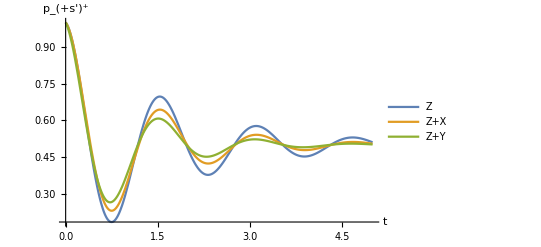

```mathematica
Plot[{fidppZ[t,2,.1,γ2,.2],fidppZX[t,2,.1,γ2,.2,.1,.1,γ3x],fidppZY[t,2,.1,γ2,.2,.1,.1,.1]},{t,0,5},PlotRange->All,PlotLegends->{"Z","Z+X","Z+Y"},AxesLabel->{t,"p_(+s')^+"},LabelStyle->Directive[FontSize->24,FontFamily->"Times"]]
```

## Dephasing plus X and Y - flips (this takes forever to evaluate; refrain)

Results for the H^+ Hamiltonian with bit and Y flips:

Results for the |++> initial state:

```mathematica
rhototpp[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,γ1x,γ2x,γ3x,γ1y,γ2y,γ3y][[i,j]],rho[0][[i,j]]==rhopp[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t]
```

$Aborted

```mathematica
solrhopp[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototpp[t])[[1]];
solrhopp[t]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
rhoSpp[t_]=TrB[solrhopp[t]]//FullSimplify;
rhoSpp[t]//MatrixForm
```

(1/2 | 1/2 ⅇ^(-t (2 γ1+γ1y+γ2y+2 (γ3+γ3y))) (Cosh[t √(-4 J^2+(γ1y-γ2y)^2)]+((-γ1y+γ2y) Sinh[t √(-4 J^2+(γ1y-γ2y)^2)])/(√(-4 J^2+(γ1y-γ2y)^2)))
1/2 ⅇ^(-t (2 γ1+γ1y+γ2y+2 (γ3+γ3y))) (Cosh[t √(-4 J^2+(γ1y-γ2y)^2)]+((-γ1y+γ2y) Sinh[t √(-4 J^2+(γ1y-γ2y)^2)])/(√(-4 J^2+(γ1y-γ2y)^2))) | 1/2)

```mathematica
fidpp[t_]=ketp.rhoSpp[t].ketp//FullSimplify
```

1/2+1/2 ⅇ^(-t (2 γ1+γ1y+γ2y+2 (γ3+γ3y))) (Cosh[t √(-4 J^2+(γ1y-γ2y)^2)]+((-γ1y+γ2y) Sinh[t √(-4 J^2+(γ1y-γ2y)^2)])/(√(-4 J^2+(γ1y-γ2y)^2)))

```mathematica
fidpp[0]
```

1

Results for the |+0> initial state:

```mathematica
rhototp0[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,γ1x,γ2x,γ3x,γ1y,γ2y,γ3y][[i,j]],rho[0][[i,j]]==rhop0[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
```

```mathematica
solrhop0[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototp0[t])[[1]];
```

```mathematica
solrhop0[t]//MatrixForm
```

```mathematica
rhoSp0[t_]=TrB[solrhop0[t]];
rhoSp0[t]//MatrixForm
```

```mathematica
fidp0[t_]=FullSimplify[ketp.rhoSp0[t].ketp]
```

```mathematica
fidpp[1]-fidp0[1]
```

## Dephasing plus amplitude damping

Redefining the decoherence Lindbladian here for convenience using the amplitude damping Lindblad terms so don' t need to introduce even more parameters :

```mathematica
Decohere[H_,ρ_,γ1_,γ2_,γ3_,γ1d_,γ2d_,γ3d_,γ1y_,γ2y_,γ3y_]:=-I Comm[H,ρ]+γ1 Lind[L1,ρ]+γ2 Lind[L2,ρ]+γ3 Lind[L12,ρ]+γ1d Lind[L1d,ρ]+γ2d Lind[L2d,ρ]+γ3d Lind[L12d,ρ]+γ1y Lind[L1y,ρ]+γ2y Lind[L2y,ρ]+γ3y Lind[L12y,ρ];
```

Results for the |++> initial state:

```mathematica
rhototpp[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,γ1d,γ2d,γ3d,0,0,0][[i,j]],rho[0][[i,j]]==rhopp[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
```

```mathematica
solrhopp[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototpp[t])[[1]];
solrhopp[t]//MatrixForm
```

((ⅇ^(-t γ1d-t γ2d) (-2 ⅇ^(t γ1d) γ1d γ2d-2 ⅇ^(t γ2d) γ1d γ2d+4 ⅇ^(t γ1d+t γ2d) γ1d γ2d+ⅇ^(t γ1d+t γ2d+t (-γ1d-γ2d-γ3d)) γ1d γ2d-2 ⅇ^(t γ1d) γ1d γ3d-ⅇ^(t γ2d) γ1d γ3d+4 ⅇ^(t γ1d+t γ2d) γ1d γ3d-ⅇ^(t γ1d) γ2d γ3d-2 ⅇ^(t γ2d) γ2d γ3d+4 ⅇ^(t γ1d+t γ2d) γ2d γ3d-ⅇ^(t γ1d) γ3d^2-ⅇ^(t γ2d) γ3d^2+4 ⅇ^(t γ1d+t γ2d) γ3d^2-ⅇ^(t γ1d+t γ2d+t (-γ1d-γ2d-γ3d)) γ3d^2))/(4 (γ1d+γ3d) (γ2d+γ3d)) | (-2 ⅇ^(1/2 t (-2 γ1d-4 γ2-γ2d-4 γ3-γ3d)) γ1d Cos[t (2 J-Δ)]-8 ⅈ ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) J Cos[t (2 J+Δ)]+4 ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) γ1d Cos[t (2 J+Δ)]+ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) γ3d Cos[t (2 J+Δ)]-2 ⅈ ⅇ^(1/2 t (-2 γ1d-4 γ2-γ2d-4 γ3-γ3d)) γ1d Sin[t (2 J-Δ)]-8 ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) J Sin[t (2 J+Δ)]-4 ⅈ ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) γ1d Sin[t (2 J+Δ)]-ⅈ ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) γ3d Sin[t (2 J+Δ)])/(4 (-8 ⅈ J+2 γ1d+γ3d)) | (-8 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) J Cos[2 J t]+4 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ2d Cos[2 J t]-2 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) γ2d Cos[2 J t]+ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ3d Cos[2 J t]-8 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) J Sin[2 J t]-4 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ2d Sin[2 J t]-2 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) γ2d Sin[2 J t]-ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ3d Sin[2 J t])/(4 (-8 ⅈ J+2 γ2d+γ3d)) | 1/4 ⅇ^(-2 t γ1-(t γ1d)/2-2 t γ2-(t γ2d)/2-(t γ3d)/2-ⅈ t Δ)
(-2 ⅇ^(1/2 t (-2 γ1d-4 γ2-γ2d-4 γ3-γ3d)) γ1d Cos[t (2 J-Δ)]+8 ⅈ ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) J Cos[t (2 J+Δ)]+4 ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) γ1d Cos[t (2 J+Δ)]+ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) γ3d Cos[t (2 J+Δ)]+2 ⅈ ⅇ^(1/2 t (-2 γ1d-4 γ2-γ2d-4 γ3-γ3d)) γ1d Sin[t (2 J-Δ)]-8 ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) J Sin[t (2 J+Δ)]+4 ⅈ ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) γ1d Sin[t (2 J+Δ)]+ⅈ ⅇ^(1/2 t (-4 γ2-γ2d-4 γ3)) γ3d Sin[t (2 J+Δ)])/(4 (8 ⅈ J+2 γ1d+γ3d)) | -(ⅇ^(-t γ2d) (-2 γ1d+ⅇ^(t γ2d+t (-γ1d-γ2d-γ3d)) γ1d-γ3d))/(4 (γ1d+γ3d)) | 1/4 ⅇ^(-2 t γ1-(t γ1d)/2-2 t γ2-(t γ2d)/2+ⅈ t Δ) | 1/4 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) (Cos[2 J t]+ⅈ Sin[2 J t])
(8 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) J Cos[2 J t]+4 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ2d Cos[2 J t]-2 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) γ2d Cos[2 J t]+ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ3d Cos[2 J t]-8 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) J Sin[2 J t]+4 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ2d Sin[2 J t]+2 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) γ2d Sin[2 J t]+ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ3d Sin[2 J t])/(4 (8 ⅈ J+2 γ2d+γ3d)) | 1/4 ⅇ^(-2 t γ1-(t γ1d)/2-2 t γ2-(t γ2d)/2-ⅈ t Δ) | -(ⅇ^(-t γ1d) (-2 γ2d+ⅇ^(t γ1d+t (-γ1d-γ2d-γ3d)) γ2d-γ3d))/(4 (γ2d+γ3d)) | 1/4 ⅇ^(1/2 t (-2 γ1d-4 γ2-γ2d-4 γ3-γ3d)) (Cos[t (2 J-Δ)]+ⅈ Sin[t (2 J-Δ)])
1/4 ⅇ^(-2 t γ1-(t γ1d)/2-2 t γ2-(t γ2d)/2-(t γ3d)/2+ⅈ t Δ) | 1/4 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) (Cos[2 J t]-ⅈ Sin[2 J t]) | 1/4 ⅇ^(1/2 t (-2 γ1d-4 γ2-γ2d-4 γ3-γ3d)) (Cos[t (2 J-Δ)]-ⅈ Sin[t (2 J-Δ)]) | 1/4 ⅇ^(t (-γ1d-γ2d-γ3d)))

```mathematica
rhoSpp[t_]=TrB[solrhopp[t]];
rhoSpp[t]//MatrixForm
```

(-(ⅇ^(-t γ2d) (-2 γ1d+ⅇ^(t γ2d+t (-γ1d-γ2d-γ3d)) γ1d-γ3d))/(4 (γ1d+γ3d))+(ⅇ^(-t γ1d-t γ2d) (-2 ⅇ^(t γ1d) γ1d γ2d-2 ⅇ^(t γ2d) γ1d γ2d+4 ⅇ^(t γ1d+t γ2d) γ1d γ2d+ⅇ^(t γ1d+t γ2d+t (-γ1d-γ2d-γ3d)) γ1d γ2d-2 ⅇ^(t γ1d) γ1d γ3d-ⅇ^(t γ2d) γ1d γ3d+4 ⅇ^(t γ1d+t γ2d) γ1d γ3d-ⅇ^(t γ1d) γ2d γ3d-2 ⅇ^(t γ2d) γ2d γ3d+4 ⅇ^(t γ1d+t γ2d) γ2d γ3d-ⅇ^(t γ1d) γ3d^2-ⅇ^(t γ2d) γ3d^2+4 ⅇ^(t γ1d+t γ2d) γ3d^2-ⅇ^(t γ1d+t γ2d+t (-γ1d-γ2d-γ3d)) γ3d^2))/(4 (γ1d+γ3d) (γ2d+γ3d)) | 1/4 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) (Cos[2 J t]+ⅈ Sin[2 J t])+(-8 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) J Cos[2 J t]+4 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ2d Cos[2 J t]-2 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) γ2d Cos[2 J t]+ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ3d Cos[2 J t]-8 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) J Sin[2 J t]-4 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ2d Sin[2 J t]-2 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) γ2d Sin[2 J t]-ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ3d Sin[2 J t])/(4 (-8 ⅈ J+2 γ2d+γ3d))
1/4 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) (Cos[2 J t]-ⅈ Sin[2 J t])+(8 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) J Cos[2 J t]+4 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ2d Cos[2 J t]-2 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) γ2d Cos[2 J t]+ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ3d Cos[2 J t]-8 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) J Sin[2 J t]+4 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ2d Sin[2 J t]+2 ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) γ2d Sin[2 J t]+ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) γ3d Sin[2 J t])/(4 (8 ⅈ J+2 γ2d+γ3d)) | 1/4 ⅇ^(t (-γ1d-γ2d-γ3d))-(ⅇ^(-t γ1d) (-2 γ2d+ⅇ^(t γ1d+t (-γ1d-γ2d-γ3d)) γ2d-γ3d))/(4 (γ2d+γ3d)))

```mathematica
fidpp[t_]=ketp.rhoSpp[t].ketp//FullSimplify
```

1/4 (2+(ⅇ^(-1/2 t (4 γ1+γ1d+2 γ2d+4 γ3+γ3d)) ((64 J^2+2 γ2d γ3d+γ3d^2+ⅇ^(t γ2d+(t γ3d)/2) (64 J^2+(2 γ2d+γ3d) (4 γ2d+γ3d))) Cos[2 J t]+16 (1+ⅇ^(t γ2d+(t γ3d)/2)) J γ2d Sin[2 J t]))/(64 J^2+(2 γ2d+γ3d)^2))

```mathematica
fidpp[0]//FullSimplify
```

1

```mathematica
FullSimplify[fidpp[t]-(1/2+1/((8J)^2+r^2)ⅇ^(-t (2( γ1+γ3)+γ1d/2)) ((1+ⅇ^(-t r/2))(1/4 Cos[2J t]   (8J)^2+4Sin[2J t]  J γ2d)+1/4 Cos[2J t] r (γ3d ⅇ^(-t r/2)+ 4γ2d+γ3d))/.{r->(2γ2d+γ3d)})]
```

0

```mathematica
fidppZD[t_,J_,γ1_,γ2_,γ3_,γ1d_,γ2d_,γ3d_](*=fidpp[t]*):=Evaluate[1/2+1/((8J)^2+r^2)ⅇ^(-t (2( γ1+γ3)+γ1d/2)) ((1+ⅇ^(-t r/2))(1/4 Cos[2J t]   (8J)^2+4Sin[2J t]  J γ2d)+1/4 Cos[2J t] r (γ3d ⅇ^(-t r/2)+ 4γ2d+γ3d))/.{r->(2γ2d+γ3d)}]
```

Results for the |+0> initial state:

```mathematica
rhototp0[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,γ1d,γ2d,γ3d,0,0,0][[i,j]],rho[0][[i,j]]==rhop0[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
```

```mathematica
solrhop0[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototp0[t])[[1]];
```

```mathematica
solrhop0[t]//MatrixForm
```

(1/2 ⅇ^(-t γ1d) (-1+2 ⅇ^(t γ1d)) | 0 | 1/2 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) (Cos[2 J t]-ⅈ Sin[2 J t]) | 0
0 | 0 | 0 | 0
1/2 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) (Cos[2 J t]+ⅈ Sin[2 J t]) | 0 | ⅇ^(-t γ1d)/2 | 0
0 | 0 | 0 | 0)

```mathematica
rhoSp0[t_]=TrB[solrhop0[t]];
rhoSp0[t]//MatrixForm
```

(1/2 ⅇ^(-t γ1d) (-1+2 ⅇ^(t γ1d)) | 1/2 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) (Cos[2 J t]-ⅈ Sin[2 J t])
1/2 ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) (Cos[2 J t]+ⅈ Sin[2 J t]) | ⅇ^(-t γ1d)/2)

```mathematica
fidp0[t_]=FullSimplify[ketp.rhoSp0[t].ketp]
```

1/2 (1+ⅇ^(-1/2 t (4 γ1+γ1d+4 γ3)) Cos[2 J t])

```mathematica
fidp0[0]//FullSimplify
```

1

```mathematica
fidp0ZD[t_,J_,γ1_,γ2_,γ3_,γ1d_,γ2d_,γ3d_](*=fidp0[t]*):=1/2 (1+ⅇ^(-1/2 t (4 γ1+γ1d+4 γ3)) Cos[2 J t])
```

Results for the |+1> initial state:

```mathematica
rhototp1[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,γ1d,γ2d,γ3d,0,0,0][[i,j]],rho[0][[i,j]]==rhop1[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
```

```mathematica
solrhop1[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototp1[t])[[1]];
solrhop1[t]//MatrixForm
```

((ⅇ^(-t γ1d-t γ2d) (-2 ⅇ^(t γ1d) γ1d γ2d-ⅇ^(t γ2d) γ1d γ2d+2 ⅇ^(t γ1d+t γ2d) γ1d γ2d+ⅇ^(t γ1d+t γ2d+t (-γ1d-γ2d-γ3d)) γ1d γ2d-2 ⅇ^(t γ1d) γ1d γ3d+2 ⅇ^(t γ1d+t γ2d) γ1d γ3d-ⅇ^(t γ1d) γ2d γ3d-ⅇ^(t γ2d) γ2d γ3d+2 ⅇ^(t γ1d+t γ2d) γ2d γ3d-ⅇ^(t γ1d) γ3d^2+2 ⅇ^(t γ1d+t γ2d) γ3d^2-ⅇ^(t γ1d+t γ2d+t (-γ1d-γ2d-γ3d)) γ3d^2))/(2 (γ1d+γ3d) (γ2d+γ3d)) | 0 | (γ2d (ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) Cos[2 J t]-ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) Cos[2 J t]-ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) Sin[2 J t]-ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) Sin[2 J t]))/(-8 ⅈ J+2 γ2d+γ3d) | 0
0 | -(ⅇ^(-t γ2d) (-2 γ1d+ⅇ^(t γ2d+t (-γ1d-γ2d-γ3d)) γ1d-γ3d))/(2 (γ1d+γ3d)) | 0 | 1/2 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) (Cos[2 J t]+ⅈ Sin[2 J t])
(γ2d (ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) Cos[2 J t]-ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) Cos[2 J t]+ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) Sin[2 J t]+ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) Sin[2 J t]))/(8 ⅈ J+2 γ2d+γ3d) | 0 | -(ⅇ^(-t γ1d) (-1+ⅇ^(t γ1d+t (-γ1d-γ2d-γ3d))) γ2d)/(2 (γ2d+γ3d)) | 0
0 | 1/2 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) (Cos[2 J t]-ⅈ Sin[2 J t]) | 0 | 1/2 ⅇ^(t (-γ1d-γ2d-γ3d)))

```mathematica
rhoSp1[t_]=TrB[solrhop1[t]];
rhoSp1[t]//MatrixForm
```

(-(ⅇ^(-t γ2d) (-2 γ1d+ⅇ^(t γ2d+t (-γ1d-γ2d-γ3d)) γ1d-γ3d))/(2 (γ1d+γ3d))+(ⅇ^(-t γ1d-t γ2d) (-2 ⅇ^(t γ1d) γ1d γ2d-ⅇ^(t γ2d) γ1d γ2d+2 ⅇ^(t γ1d+t γ2d) γ1d γ2d+ⅇ^(t γ1d+t γ2d+t (-γ1d-γ2d-γ3d)) γ1d γ2d-2 ⅇ^(t γ1d) γ1d γ3d+2 ⅇ^(t γ1d+t γ2d) γ1d γ3d-ⅇ^(t γ1d) γ2d γ3d-ⅇ^(t γ2d) γ2d γ3d+2 ⅇ^(t γ1d+t γ2d) γ2d γ3d-ⅇ^(t γ1d) γ3d^2+2 ⅇ^(t γ1d+t γ2d) γ3d^2-ⅇ^(t γ1d+t γ2d+t (-γ1d-γ2d-γ3d)) γ3d^2))/(2 (γ1d+γ3d) (γ2d+γ3d)) | 1/2 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) (Cos[2 J t]+ⅈ Sin[2 J t])+(γ2d (ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) Cos[2 J t]-ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) Cos[2 J t]-ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) Sin[2 J t]-ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) Sin[2 J t]))/(-8 ⅈ J+2 γ2d+γ3d)
1/2 ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) (Cos[2 J t]-ⅈ Sin[2 J t])+(γ2d (ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) Cos[2 J t]-ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) Cos[2 J t]+ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-4 γ3)) Sin[2 J t]+ⅈ ⅇ^(1/2 t (-4 γ1-γ1d-2 γ2d-4 γ3-γ3d)) Sin[2 J t]))/(8 ⅈ J+2 γ2d+γ3d) | 1/2 ⅇ^(t (-γ1d-γ2d-γ3d))-(ⅇ^(-t γ1d) (-1+ⅇ^(t γ1d+t (-γ1d-γ2d-γ3d))) γ2d)/(2 (γ2d+γ3d)))

```mathematica
fidp1[t_]=ketp.rhoSp1[t].ketp//FullSimplify
```

(64 J^2+(2 γ2d+γ3d)^2+ⅇ^(-1/2 t (4 γ1+γ1d+2 γ2d+4 γ3+γ3d)) ((64 J^2+(2 γ2d+γ3d) (2 ⅇ^(t γ2d+(t γ3d)/2) γ2d+γ3d)) Cos[2 J t]+16 (1+ⅇ^(t γ2d+(t γ3d)/2)) J γ2d Sin[2 J t]))/(2 (64 J^2+(2 γ2d+γ3d)^2))

```mathematica
fidp1[0]//FullSimplify
```

1

```mathematica
FullSimplify[fidp1[t]-1/2(1+ⅇ^(- t (2(γ1+γ3)+γ1d/2)) (((8J)^2 ⅇ^(-1/2 t r)+r (2 γ2d+γ3d ⅇ^(-1/2 t r))) Cos[2 J t]+16 (ⅇ^(-1/2 t r)+1) J γ2d Sin[2 J t])/((8J)^2+r^2))/.{r->(2γ2d+γ3d)}]
```

0

```mathematica
fidp1ZD[t_,J_,γ1_,γ2_,γ3_,γ1d_,γ2d_,γ3d_](*=fidp0[t]*):=Evaluate[1/2(1+ⅇ^(- t (2(γ1+γ3)+γ1d/2)) (((8J)^2 ⅇ^(-1/2 t r)+r (2 γ2d+γ3d ⅇ^(-1/2 t r))) Cos[2 J t]+16 (ⅇ^(-1/2 t r)+1) J γ2d Sin[2 J t])/((8J)^2+r^2))/.{r->(2γ2d+γ3d)}]
```

```mathematica
funcfidpp[t_,J_,γ1_,γ3_,γ1d_,γ2d_,γ3d_](*=fidpp[t]*)=1/8 (4+1/(64 J^2+(2 γ2d+γ3d)^2)ⅇ^(-1/2 t (4 ⅈ J+4 γ1+γ1d+2 γ2d+4 γ3+γ3d)) (64 (1+ⅇ^(4 ⅈ J t)) (1+ⅇ^(t γ2d+(t γ3d)/2)) J^2-16 ⅈ (-1+ⅇ^(4 ⅈ J t)) (1+ⅇ^(t γ2d+(t γ3d)/2)) J γ2d+(1+ⅇ^(4 ⅈ J t)) (2 γ2d+γ3d) (γ3d+ⅇ^(t γ2d+(t γ3d)/2) (4 γ2d+γ3d))));
funcfidp0[t_,J_,γ1_,γ3_,γ1d_,γ2d_,γ3d_](*=fidp0[t]*)=1/4 (2+ⅇ^(-1/2 t (4 ⅈ J+4 γ1+γ1d+4 γ3)) (1+ⅇ^(4 ⅈ J t)));
funcfidp1[t_,J_,γ1_,γ3_,γ1d_,γ2d_,γ3d_](*=fidp1[t]*)=1/(2 (64 J^2+(2 γ2d+γ3d)^2))(64 J^2+(2 γ2d+γ3d)^2+ⅇ^(-1/2 t (4 γ1+γ1d+2 γ2d+4 γ3+γ3d)) ((64 J^2+(2 γ2d+γ3d) (2 ⅇ^(t γ2d+(t γ3d)/2) γ2d+γ3d)) Cos[2 J t]+16 (1+ⅇ^(t γ2d+(t γ3d)/2)) J γ2d Sin[2 J t]));
```

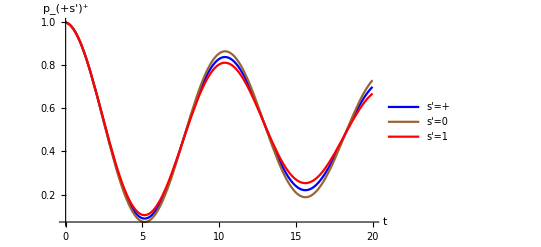

pplot.jpg

```mathematica
Plot[{fidppZD[t,.3,.01,.0025,.01,.01,.01],fidp0ZD[t,.3,.01,.0025,.01,.01,.01],fidp1ZD[t,.3,.01,.0025,.01,.01,.01]},{t,0,20},PlotRange->All,PlotLegends->{"s'=+","s'=0","s'=1"},AxesLabel->{t,"p_(+s')^+"},LabelStyle->Directive[FontSize->24,FontFamily->"Times"],PlotStyle->{Blue,Brown,Red}]
Export["pplot.jpg",%]
```

```mathematica
Animate[Plot[{fidppZD[t,1,.1x,x/2,x/4,x/4,x],fidp0ZD[t,1,.1x,x/2,x/4,x/4,x],fidp1ZD[t,1,.1x,x/2,x/4,x/4,x]},{t,0,6},PlotRange->All,PlotLegends->{"s'=+","s'=0","s'=1"},AxesLabel->{t,"p_(+s')^+"},LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Brown,Red}],{x,0,.5},AnimationRunning->False]
```

## Dephasing plus amplitude damping plus Y-flips

Redefining the decoherence Lindbladian here for convenience so don' t need to introduce even more parameters :

Results for the |++> initial state:

```mathematica
rhototpp[t]=DSolve[Table[{D[rho[t][[i,j]],t]==Decohere[Hp,rho[t],γ1,γ2,γ3,γ1d,γ2d,γ3d,γ1y,γ2y,γ3y][[i,j]],rho[0][[i,j]]==rhopp[[i,j]]},{i,4},{j,4}]//Flatten,Table[rho[t][[i,j]],{i,4},{j,4}]//Flatten,t];
```

```mathematica
solrhopp[t_]=({{r11[t],r12[t],r13[t],r14[t]},{r21[t],r22[t],r23[t],r24[t]},{r31[t],r32[t],r33[t],r34[t]},{r41[t],r42[t],r43[t],r44[t]}}/.rhototpp[t])[[1]];
solrhopp[t]//MatrixForm
```